```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"interp_quarks_udud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

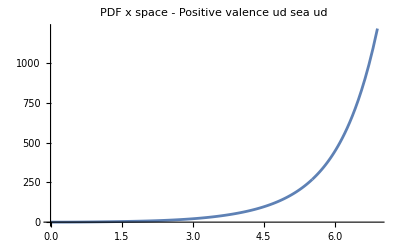

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF x space - Positive valence ud sea ud",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Abs_Fourier_udud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

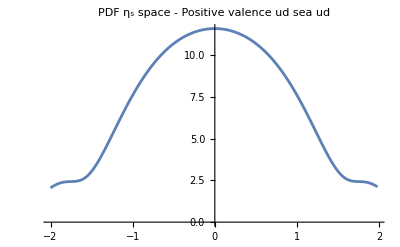

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space - Positive valence ud sea ud",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Abs_Fourier_udud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

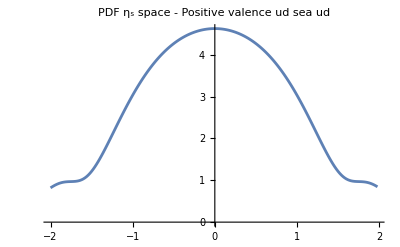

```mathematica
ListLinePlot[Transpose[{col1,1/(√(2 π))*col2}],PlotLabel->"PDF η_s space - Positive valence ud sea ud",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

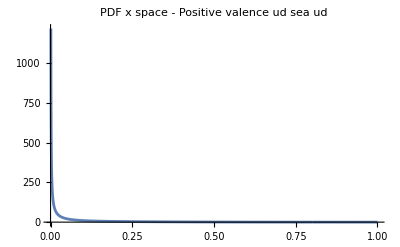

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF x space - Positive valence ud sea ud",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

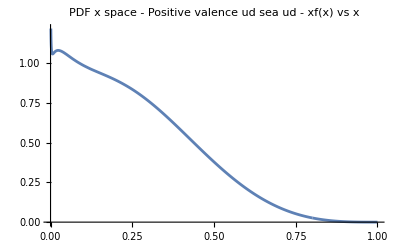

```mathematica
ListLinePlot[Transpose[{col1,col1*col2}],PlotLabel->"PDF x space - Positive valence ud sea ud - xf(x) vs x",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

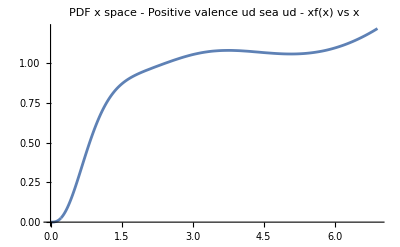

```mathematica
ListLinePlot[Transpose[{-Log[col1],col1*col2}],PlotLabel->"PDF x space - Positive valence ud sea ud - xf(x) vs x",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

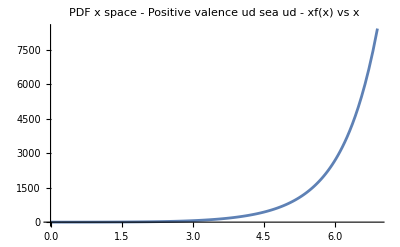

```mathematica
ListLinePlot[Transpose[{-Log[col1],-Log[col1]*col2}],PlotLabel->"PDF x space - Positive valence ud sea ud - xf(x) vs x",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

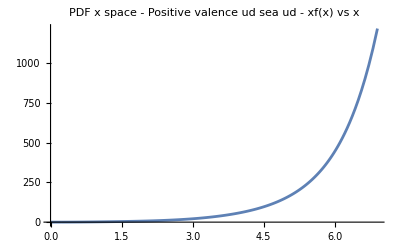

```mathematica
ListLinePlot[Transpose[{-Log[col1],col2}],PlotLabel->"PDF x space - Positive valence ud sea ud - xf(x) vs x",PlotRange->All]
```